[Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x-y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x+y/2]ⅆy];
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]-p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (-x Cos[θ]+p Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after heterodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]+s Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]);

W2modeAlphaproj[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=∫_(-∞)^∞ ∫_(-∞)^∞ W2mode[t,r,α,θ,x1,p1,x,p,s]((ⅇ^(-((x-x1)^2+(p-p1)^2)/2))/(2π))ⅆxⅆp
```

```mathematica
ClearAll[t,r,α,x1,p1,x2,p2];
W2modeAlphaproj[t,r,α,0,x1,p1,x2,p2,1]
```

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (ⅇ^(-p^2-p2^2-x^2-x2^2)1/π^2(ⅇ^(-2 α^2)(ⅇ^(+2 √2 t α (x Cos[0]-p Sin[0])-2 √2 r α (p2 Cos[0]+x2 Sin[0]))+ⅇ^(+2 √2 t α (-x Cos[0]+p Sin[0])+2 √2 r α (p2 Cos[0]+x2 Sin[0])))+(ⅇ^(-2 ⅈ √2 r α (x2 Cos[0]-p2 Sin[0])-2 ⅈ √2 t α (p Cos[0]+x Sin[0]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[0]-p2 Sin[0])+2 ⅈ √2 t α (p Cos[0]+x Sin[0])))))((ⅇ^(-((x-x1)^2+(p-p1)^2)/2))/(2π))ⅆxⅆp
```

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(3 π^2)ⅇ^(1/3 (-p1^2-3 p2^2-x1^2-3 x2^2-6 √2 p2 r α-2 ⅈ √2 p1 t α-2 √2 t x1 α-6 ⅈ √2 r x2 α-6 α^2-4 t^2 α^2)) (ⅇ^(2/3 α (3 √2 p2 r+√2 t x1+3 α))+ⅇ^(2/3 α (3 √2 p2 r+2 ⅈ √2 p1 t+√2 t x1+6 ⅈ √2 r x2+3 α))+ⅇ^(2/3 α (6 √2 p2 r+ⅈ √2 p1 t+3 ⅈ √2 r x2+4 t^2 α))+ⅇ^(2/3 α (ⅈ √2 p1 t+2 √2 t x1+3 ⅈ √2 r x2+4 t^2 α))))ⅆx1ⅆp1ⅆx2ⅆp2
```

```mathematica
2 (ⅇ^(2 (-1+r^2+t^2) α^2)+ⅇ^(-2 (r^2+t^2) α^2))/.r^2+t^2->1
```

2 (1+ⅇ^(-2 α^2))

```mathematica
(1/(3 π^2)ⅇ^(1/3 (-p1^2-3 p2^2-x1^2-3 x2^2-6 √2 p2 r α-2 ⅈ √2 p1 t α-2 √2 t x1 α-6 ⅈ √2 r x2 α-6 α^2-4 t^2 α^2)) (ⅇ^(2/3 α (3 √2 p2 r+√2 t x1+3 α))+ⅇ^(2/3 α (3 √2 p2 r+2 ⅈ √2 p1 t+√2 t x1+6 ⅈ √2 r x2+3 α))+ⅇ^(2/3 α (6 √2 p2 r+ⅈ √2 p1 t+3 ⅈ √2 r x2+4 t^2 α))+ⅇ^(2/3 α (ⅈ √2 p1 t+2 √2 t x1+3 ⅈ √2 r x2+4 t^2 α))))/.{x2->ρ Cos[ϕ],p2->ρ Sin[ϕ]}
```

```mathematica
Simplify[1/(3 π^2)ⅇ^(1/3 (-p1^2-x1^2-2 ⅈ √2 p1 t α-2 √2 t x1 α-6 α^2-4 t^2 α^2-6 ⅈ √2 r α ρ Cos[ϕ]-3 ρ^2 Cos[ϕ]^2-6 √2 r α ρ Sin[ϕ]-3 ρ^2 Sin[ϕ]^2)) (ⅇ^(2/3 α (ⅈ √2 p1 t+2 √2 t x1+4 t^2 α+3 ⅈ √2 r ρ Cos[ϕ]))+ⅇ^(2/3 α (√2 t x1+3 α+3 √2 r ρ Sin[ϕ]))+ⅇ^(2/3 α (2 ⅈ √2 p1 t+√2 t x1+3 α+6 ⅈ √2 r ρ Cos[ϕ]+3 √2 r ρ Sin[ϕ]))+ⅇ^(2/3 α (ⅈ √2 p1 t+4 t^2 α+3 ⅈ √2 r ρ Cos[ϕ]+6 √2 r ρ Sin[ϕ])))]
```

1/(3 π^2)ⅇ^(1/3 (-p1^2-x1^2-4 t^2 α^2-3 ρ^2)) (ⅇ^(-2/3 ⅈ √2 α (p1 t+3 r ρ Cos[ϕ]))+ⅇ^(2/3 ⅈ √2 α (p1 t+3 r ρ Cos[ϕ]))+ⅇ^(2/3 α (√2 t x1-3 α+4 t^2 α-3 √2 r ρ Sin[ϕ]))+ⅇ^(2/3 α (-√2 t x1-3 α+4 t^2 α+3 √2 r ρ Sin[ϕ])))

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ ∫_0^(2π) ∫_0^∞ (1/(3 π^2)ⅇ^(1/3 (-p1^2-x1^2-4 t^2 α^2-3 ρ^2)) (ⅇ^(-2/3 ⅈ √2 α (p1 t+3 r ρ Cos[ϕ]))+ⅇ^(2/3 ⅈ √2 α (p1 t+3 r ρ Cos[ϕ]))+ⅇ^(2/3 α (√2 t x1-3 α+4 t^2 α-3 √2 r ρ Sin[ϕ]))+ⅇ^(2/3 α (-√2 t x1-3 α+4 t^2 α+3 √2 r ρ Sin[ϕ]))))ρ ⅆρⅆϕⅆx1ⅆp1
```

$Aborted

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(3 π^2)ⅇ^(1/3 (-p1^2-3 p2^2-x1^2-3 x2^2-6 √2 p2 r α-2 ⅈ √2 p1 t α-2 √2 t x1 α-6 ⅈ √2 r x2 α-6 α^2-4 t^2 α^2)) (ⅇ^(2/3 α (3 √2 p2 r+√2 t x1+3 α))+ⅇ^(2/3 α (3 √2 p2 r+2 ⅈ √2 p1 t+√2 t x1+6 ⅈ √2 r x2+3 α))+ⅇ^(2/3 α (6 √2 p2 r+ⅈ √2 p1 t+3 ⅈ √2 r x2+4 t^2 α))+ⅇ^(2/3 α (ⅈ √2 p1 t+2 √2 t x1+3 ⅈ √2 r x2+4 t^2 α))))ⅆx1ⅆp1ⅆx2ⅆp2
```

#### Odd cat

$Aborted

```mathematica
(* Numerator for odd cat *)∫_(-∞)^∞ (ⅇ^(-(((x-x0)^2+(p-p0)^2)/2)))/(2π)((ⅇ^(-p1^2-p2^2-x1^2-x2^2-2  α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))-(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2
```

(ⅇ^(-p1^2-x1^2-x2^2-2 α^2+2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 α^2-2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2+2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2-2 ⅈ √2 (p1 t+r x2) α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2+2 ⅈ √2 (p1 t+r x2) α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)

```mathematica
Simplify[(ⅇ^(-p1^2-x1^2-x2^2-2 α^2+2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 α^2-2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2+2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2-2 ⅈ √2 (p1 t+r x2) α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2+2 ⅈ √2 (p1 t+r x2) α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2),{r^2+t^2==1}]
```

1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))-ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))-ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))))

```mathematica
(* After tracing out the momentum in mode 2 for odd cat *)
Wbhnumer[t_,r_,α_,θ_,x1_,p1_,x2_]:=1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))-ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))-ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))));
```

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
ClearAll[t,r,α,Δ, θ]
∫_(-∞)^∞ Wbhnumer[t,r,α,θ, x1,p1,x2]ⅆx2
```

1/π ⅇ^(-p1^2-x1^2-2 √2 t (ⅈ p1+x1) α Cos[θ]-2 (r^2+t^2) α^2 Cos[θ]^2-2 √2 t (p1+ⅈ x1) α Sin[θ]-2 α^2 Sin[θ]^2) (-ⅇ^(2 t α (t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 α (r^2 α+ⅈ √2 p1 t Cos[θ]+√2 t (2 p1+ⅈ x1) Sin[θ]))-ⅇ^(2 t α (t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (r^2 α+√2 t (ⅈ p1+2 x1) Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
Simplify[1/π ⅇ^(-p1^2-x1^2-2 √2 t (ⅈ p1+x1) α Cos[θ]-2 (r^2+t^2) α^2 Cos[θ]^2-2 √2 t (p1+ⅈ x1) α Sin[θ]-2 α^2 Sin[θ]^2) (-ⅇ^(2 t α (t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 α (r^2 α+ⅈ √2 p1 t Cos[θ]+√2 t (2 p1+ⅈ x1) Sin[θ]))-ⅇ^(2 t α (t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (r^2 α+√2 t (ⅈ p1+2 x1) Cos[θ]+ⅈ √2 t x1 Sin[θ]))),r^2+t^2==1]
```

1/π ⅇ^(-p1^2-x1^2-2 α^2-2 t^2 α^2-2 √2 t α ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))-ⅇ^(2 t α (2 t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (α+√2 t (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))+ⅇ^(2 α (α+√2 t ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ]))))

```mathematica
∫_(-∞)^∞ (1/π ⅇ^(-p1^2-x1^2-2 α^2-2 t^2 α^2-2 √2 t α ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))-ⅇ^(2 t α (2 t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (α+√2 t (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))+ⅇ^(2 α (α+√2 t ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ])))))ⅆp1
```

1/(√π)ⅇ^(-x1^2-2 α^2-3 t^2 α^2-2 √2 t x1 α Cos[θ]-t^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
Simplify[1/(√π)ⅇ^(-x1^2-2 α^2-3 t^2 α^2-2 √2 t x1 α Cos[θ]-t^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ]))),r^2+t^2==1]
```

1/(√π)ⅇ^(-x1^2-2 α^2-t^2 α^2 (3+Cos[2 θ])-2 √2 t x1 α (Cos[θ]+ⅈ Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
∫_(-∞)^∞ (1/(√π)ⅇ^(-x1^2-2 α^2-t^2 α^2 (3+Cos[2 θ])-2 √2 t x1 α (Cos[θ]+ⅈ Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ]))))ⅆx1
```

2-2 ⅇ^(-2 α^2)

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
∫_(-Δ/2)^(Δ/2) Wbhnumer[t,r,α,θ,x1,p1,x2]ⅆx2
```

1/π^(3/2)(1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]+ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2-√2 r α Sin[θ]]+ⅇ^(2 r^2 α^2) Erf[Δ/2+√2 r α Sin[θ]])-1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]-ⅇ^(2 r^2 α^2) Erf[Δ/2-√2 r α Sin[θ]]-ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Simplify[1/π^(3/2)(1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]+ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2-√2 r α Sin[θ]]+ⅇ^(2 r^2 α^2) Erf[Δ/2+√2 r α Sin[θ]])-1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]-ⅇ^(2 r^2 α^2) Erf[Δ/2-√2 r α Sin[θ]]-ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2+√2 r α Sin[θ]])),r^2+t^2==1]
```

1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]));
```

```mathematica
(* Probability of success *)
∫_(-∞)^∞ ∫_(-∞)^∞ (1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])))ⅆx1ⅆp1
```

ⅇ^(-2 α^2) (-Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]-Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (r^2+t^2) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

[Rslt] Wigner distributions - essential code (Odd cat)

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=1/(2(1-ⅇ^(-2 α^2)))1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]));Ps[t_,r_,α_,θ_,Δ_]:= 1/(2(1-ⅇ^(-2 α^2)))(ⅇ^(-2 α^2) (-Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]-Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (r^2+t^2) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])));

WhnHomodyne[t_,α_,θ_,x1_,p1_,Δ_]:=Re[Wh[t,√(1-t^2),α,θ,x1,p1,Δ]/Ps[t,√(1-t^2),α,θ,Δ]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

(* Results for the threshold detectors obtained from iPad *)
WhnThreshold[t_,α_,θ_,x1_,p1_,η_]:=((Sinh[t^2 α^2]Cosh[(1-η)(1-t^2)α^2])/Sinh[α^2(1-η (1-t^2))])Wcat[t α,θ,x1,p1,-1]+((Cosh[t^2 α^2]Sinh[(1-η)(1-t^2)α^2])/Sinh[α^2(1-η (1-t^2))])Wcat[t α,θ,x1,p1,1];
PsThreshold[t_,α_,η_]:=Sinh[α^2(1-η (1-t^2))]/Sinh[α^2];
```

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (1/(1/(2(1-ⅇ^(-2 α^2)))(ⅇ^(-2 α^2) (-Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]-Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (1) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))))1/(2(1-ⅇ^(-2 α^2)))1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])))(((Sinh[t^2 α^2]Cosh[(1-η)r^2 α^2])/Sinh[α^2(1-η r^2)])Wcat[t α,θ,x1,p1,-1]+((Cosh[t^2 α^2]Sinh[(1-η)r^2 α^2])/Sinh[α^2(1-η r^2)])Wcat[t α,θ,x1,p1,1])ⅆx1ⅆp1
```

$Aborted

Fixing Δ finding η

Homodyne success probability:

0.165155

{η→0.984911}

Threshold success probability:

0.137123

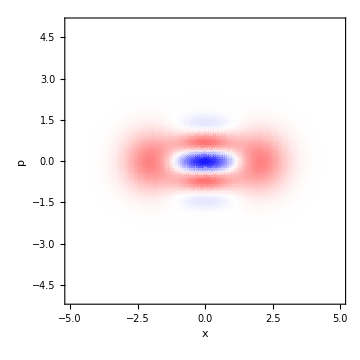
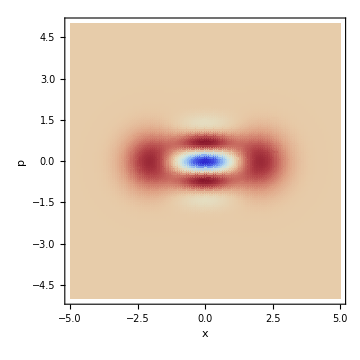
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δ,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ=0π/2;
Δ=0.3;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

(* Psuccess *)
"Homodyne success probability: "
Re[Ps[t,√(1-t^2),α,θ,Δ]]


matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Abs[ Total[matWhHomodyne,2]](limits/range)^2);

model=WhnThreshold[t,α,θ,x,p,η];
range =(Dimensions[matWhHomodyne][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhHomodyne[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]


matWhThreshold=Table[Re[Chop[WhnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold=matWhThreshold/(Abs[Total[matWhThreshold,2]](limits/range)^2);
"Threshold success probability: "
PsThreshold[t,α,η/.fit]

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(π*#+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(π*#+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

Comparing P_S for odd cat states w.r.t. θ

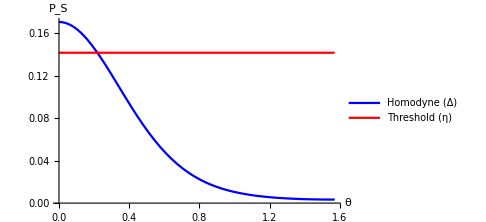

```mathematica
Plot[{Ps[t,√(1-t^2),α,θ,Δ], PsThreshold[t,α,η/.fit]},{θ,0,π/2},AxesLabel->{θ,Subscript[P, S]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->{"Homodyne (Δ)","Threshold (η)"}]
```

#### Fixing η finding Δ

```mathematica
ClearAll[η,Δ,model, fit,Data,IdxData,α,plotvalues,plots];
limits=10;
range=55;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

{ηmin,ηmax,dη}={0.1,0.9,0.1};
{αmin,αmax,dα}={1,4,0.2};

plots={};
Do[
plotvalues[{α,t}]={};
Do[
matWhThreshold=Table[Re[Chop[WhnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold=matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);

model=WhnHomodyne[t,α,θ,x,p,Δ];
    range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}];
AppendTo[plotvalues[{α,t}],{η,Δ/.fit}]
,{η,ηmin,ηmax,dη}];
AppendTo[plots,plotvalues[{α,t}]]
,{α,αmin,αmax,dα}]
```

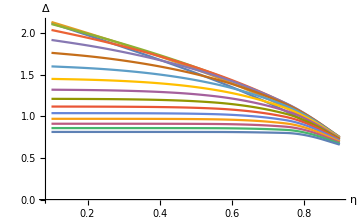

```mathematica
ListLinePlot[plots,AxesLabel->{η,Δ},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full]
```

{Δ→2.09067}

0.109775

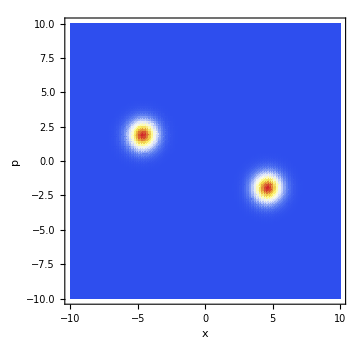
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,Δ,θ,model, fit,Data,IdxData];
limits=10;
range=55;
α=5;
θ =π/8;
η=0.5;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

matWhThreshold=Table[Re[Chop[WhnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold =matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);

model=WhnHomodyne[t,α,θ,x,p,Δ];
range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}]

Re[Ps[t,√(1-t^2),α,θ,Δ/.fit]](* Psuccess *)

matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Total[matWhHomodyne,2](limits/range)^2);

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(π*#+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(π*#+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

#### [Calc] Coefficient of the interference term

```mathematica
ClearAll[α,t,r];
Simplify[Expand[Simplify[(cp Wcat[t α,x1,p1,1]+cm Wcat[t α,x1,p1,-1])]]]
```

(ⅇ^(-p1^2-2 (x1^2+t^2 α^2)) ((cm+cp) (ⅇ^((x1-√2 t α)^2)+ⅇ^((x1+√2 t α)^2))-2 (cm-cp) ⅇ^(x1^2+4 t^2 α^2) Cos[2 √2 p1 t α]))/(2 (1+ⅇ^(2 t^2 α^2)) π)

```mathematica
(* General *)
FringeTerm=FullSimplify[ (ⅇ^(-p1^2-2 (x1^2+t^2 α^2))2 (-1+2 cp) ⅇ^(x1^2+4 t^2 α^2))/(2 (1+ⅇ^(2 t^2 α^2)) π)]
```

((-1+2 cp) ⅇ^(-p1^2-x1^2) (1+Tanh[t^2 α^2]))/(2 π)

```mathematica
ClearAll[Δ];
FringeTermHomodyne=FullSimplify[(ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2)  π ⅇ^(2 t α (√2 x1+t α))2 Im[Erfi[√2 r α+(ⅈ Δ)/2]])/(ⅇ^(-2 α^2) π^2 (2 ⅇ^(2  α^2) Erf[Δ/2]+2Im[Erfi[√2 r α+(ⅈ Δ)/2]]))]
```

(ⅇ^(-p1^2-x1^2+2 t^2 α^2) Im[Erfi[√2 r α+(ⅈ Δ)/2]])/(ⅇ^(2 α^2) π Erf[Δ/2]+π Im[Erfi[√2 r α+(ⅈ Δ)/2]])

#### Observations

-For large α, and high η it seems Δ doesn’t exist
-For  Δ > Δ_m, η doesn’t exist 
-We are projecting on infinitely squeezed states with arbitrary momentum coordinate. Does this mean ‘n’ can take high values too and so we are not heralding on zero photons?

#### Next Steps

Add the Psuccess for threshold detectors in the comparison as well .